## Inlämningsuppgift 1: Uppgift 4

Uppgift 4: Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig kommer i kapp sköldpaddan. Undersök och förklara paradoxen, samt ta fram en lösning när Akilles faktiskt kommer i kapp sköldpaddan. Visa paradoxen både numeriskt och grafiskt.

Utifrån texten ovanför har jag skrivit ned alla värden

```mathematica
Enhet för 1 meter = d
Slutmål distans uttryckt i meter Subscript[d, end] = 100
Tidsenhet per rörelse för Akilles och sköldpaddan = 10^(1-n)
Sköldpaddans hastighet  Subscript[s, v] = 8 10^(1 - n)
Akilles hastighet  Subscript[a, v]= 10 Subscript[s, v]*10^(1 - n)
Sköldpaddans startdistans Subscript[s, d0]= 80 
Akilles startdistans Subscript[a, d0] = 0
Skoldpaddans distans vid Subscript[n, 1]= 88
Akilles Distans vid Subscript[n, 1] = 80
Avstånd mellan Akilles och sköldpaddan = Subscript[d, Δ]
```

I systemet som paradoxen målar upp finns ingen konstant enhet för tid. Det är istället det antal rörelser som Akilles och sköldpaddan har rört sig sedan början n_0. 
då distansen  d_Δ minskar logaritmiskt med antalet rörelser n. 

Man kan endast måla upp paradoxen så som den är exakt skriven genom att visa d_Δ .

för 0 <= n
8*10^(1-n)== d_Δ

två godtyckliga världen för n illustrerar det minskande avståndet

```mathematica
n=1
```

8==d

```mathematica
n = 4
```

4

```mathematica
8*10^(1-n) ==d
```

1/125==d

```mathematica
Clear[n]
```

Och en grafisk lösning

```mathematica
8* 10^(1 - n) == d
```

2^(4-n) 5^(1-n)==d

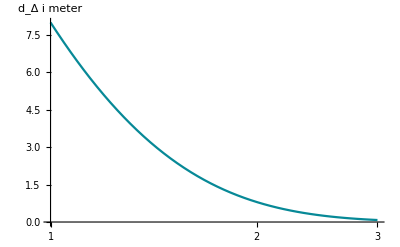

```mathematica
LogLinearPlot[8*10^(1-n),{n, 1, 3}, AxesLabel-> HoldForm[Subscript[d, Δ] i meter]]
```

Då distansen går mot 0 d_Δ != 0 kommer Akilles aldrig komma ikapp sköldpaddan.

### Att lösa den här ekvationen i verkligheten

I verkligheten så finns det en variabel som ersätter paradoxens egna.

```mathematica
En konstant tidsenhet  = n
```

Då blir det enkelt att lösa.

a_d för n_0 = 0
s_d för n_0 = 80

då a_d för n_1 = 80
s_d för n_1 = 88

och a_v= 10 s_v

kan man skriva ekvationen

```mathematica
80n=8 n+80
```

```mathematica
Reduce[80n == 8n + 80,n]
```

n==10/9

och svaret är  n==10/9 eller 1,1